# Residue Calculus

### More Plotting Stuff

I made another plotting routine.

```mathematica
ReImComplexPlot3D[ f_,{z_,R_}]:=Module[{fTemp,x,y},
fTemp[{x_,y_}]=f/.z->x+I y;
Plot3D[
{Im[fTemp[{x,y}]],Re[fTemp[{x,y}]]},
{x, -R,R},
{y,-R,R},
PlotLegends->{"im","re"}]
]
f[z_]:=ArcTan[z]
TabView[{
"CPlot3D"->ComplexPlot3D[f[z],{z,3}],
"ReImPlot3D"->ReImComplexPlot3D[f[z],{z,3}]
}]
```

12

As a reminder the residue theorem says
	∫_Γ f(z)dz=2π ⅈ   ∑_(j=1)^m w(c_j) r_j
for an analytic function f(z) with singularities at c_1,c_2,…,c_m in Γ. The residues are  r_j=lim_(z→c_j) (z-c_j)f(z) and w is the winding number.
	https://en.wikipedia.org/wiki/Residue_theorem
Chapter 5 is about the techniques that use the residue theorem to compute useful things.

## Sums: Section 5.2 p148

You know that ∑_(k=1)^∞ 1/k^2 converges from Calculus II. It looks as though it goes to something like 1.65 or so.

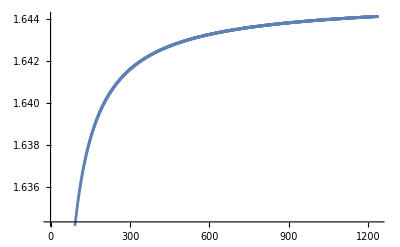

```mathematica
MaxIter=1234;
sum=0.0;
Data=Table[
sum+=1/k^2,{k,1,MaxIter}];
ListPlot[Data]
```

Mathematica somehow knows that the infinite sum.  The question for today is how? I guess the other question is can we do other interesting sums.  For instance

```mathematica
Clear[a]
Sum[1/n^2,{n,1, ∞}]
Sum[1/(n^2+a^2),{n,1, ∞}]
Sum[1/(n^4+1),{n,1, ∞}]
```

π^2/6

(-1+a π Coth[a π])/(2 a^2)

1/4 (-2+(-1)^(1/4) π Cot[(-1)^(1/4) π]+(-1)^(3/4) π Cot[(-1)^(3/4) π])

### Basic Trick

The basic trick is to create a contour integral with gives the desired sum as residues.

g(z)=π Cos[π z]/Sin[π z]=π Cot[π z] has simple poles at z=0,±1,±2,…

The residues of g(z) at all the poles z=0,±1,±2,… is 1

g(z) has easily understood behavior as im(z) gets big.

```mathematica
Residue[π Cot[π z],{z,0}]
```

1

```mathematica
Sum[1/(n^2+a^2),{n,1, ∞}]
```

```mathematica
TabView[{
"arg-abs 3D"->ComplexPlot3D[π Cot[π z],{z,3},PlotRange->{0,10},PlotLegends->Automatic],
"arg-abs 2D"->ComplexPlot[π Cot[π z],{z,3},PlotLegends->Automatic],
"re & im"->ReImComplexPlot3D[π Cot[π z],{z,3}]
}]
```

123

Sum[1/(n^2+1),{n,1, ∞}]

```mathematica
f[z_]:=π Cot[π z] 1/(z^2+1)
TabView[{
"arg-abs 3D"->ComplexPlot3D[f[z],{z,3},PlotRange->{0,10},PlotLegends->Automatic],
"arg-abs 2D"->ComplexPlot[f[z],{z,3},PlotLegends->Automatic],
"re & im"->ReImComplexPlot3D[f[z],{z,3}]
}]
```

123